# Project

## ideas and terminologies learned from the literature

Terrain models are typically constructed from gridded data, from points organized along contour strings, or from triangulated sets of scattered data points.

triangulated irregular network (TIN) models

A TIN is constructed by connecting a set of data points with edges to form a network of triangles. If the surface is assumed to vary linearly across each triangle, the TIN represents a piecewise linear interpolation of the data points.

Delauney criterion to guide the triangulation process

The Delauney criterion is satisfied when the circumcircle (the circle defined by the triangle vertices) of the three vertices forming a triangle encompasses no other vertices.

During the triangulation process, the shared edges of pairs of adjacent triangles are swapped as necessary to ensure that this criterion is satisfied.

Flow paths can be constructed from any arbitrary point on a TIN by following the path of maximum downward gradient from triangle to triangle (water will tend to follow the path of steepest descent)

The flow paths are perpendicular to the contour segments across triangles.

Flow where the path is traced from edge to edge across the face of adjacent triangles is termed "overland flow." Whenever the flow path encounters an edge whose two adjacent triangles both slope towards it, the flow path follows the triangle edge. This flow along an edge is termed "channel flow." An entire flow path is determined by following a series of overland and channel flow paths until a pit on the interior of the TIN or a boundary on the exterior is reached.

StreamPlot

## Try-and-error with Geo commands

lake Urmie geoposition

```mathematica
FromDMS["37°42'0''N 45°19'0.''E"]
```

{377/10,45.3167}

### Region with min θ_0

this is the size of a rectangular in the latitude and longitude 2D space where each point is at the center of that rectangular

```mathematica
θ0=2*0.000171661376953125;
```

θ is the final {lat. longt.} which is a factor of θ_0. The factor “n” gives the dimension of data1 ({n,n}); in other words, # f

```mathematica
θ=10θ0;
```

loca is a 2D GeoGraphicspaclet:ref/GeoGraphics primitive that represents a geo region bounded by parallels 0,θ and meridians0,θ on the surface of the Earth.

```mathematica
loca=(*GeoBoundsRegion[{{0,θ},{0,θ}}];loca2=*)GeoDisk[Entity["Mountain","MountEverest"],Quantity[100,"m"]];
```

the area of the geo region “loca”

```mathematica
√UnitConvert[GeoArea@loca,"m^2"]
```

177.245 m

### Region as a disk

loca is a 2D GeoGraphicspaclet:ref/GeoGraphics primitive that represents a geo region bounded by parallels 0,θ and meridians0,θ on the surface of the Earth.

```mathematica
loca=GeoDisk[Entity["Mountain","MountEverest"],Quantity[50,"m"]];
```

### Finding the resolution for GeoElevationData

here we decide about the format in GeoElevationData

```mathematica
format="GeoPosition";
```

GeoElevationData for the “loca” with a given “format”

```mathematica
data1=GeoElevationData[loca,Automatic,format]//Normal
ListPlot3D[Reverse@Flatten[(List@@data1)⟦1⟧,1],MeshFunctions->{#3&},Mesh->50]
Print[Style["data for "<>format<>" = ",Bold],data1//FullForm]
```

GeoPosition[…]

-Graphics3D-

data for GeoPosition = GeoPosition[List[List[List[27.9885,86.925,8714.26],List[27.9885,86.9254,8713.26],List[27.9885,86.9257,8700.26]],List[List[27.9882,86.925,8705.26],List[27.9882,86.9254,8697.26],List[27.9882,86.9257,8672.26]],List[List[27.9878,86.925,8688.25],List[27.9878,86.9254,8667.25],List[27.9878,86.9257,8638.25]]]]

### Comparison with a different format

here we decide about the format in GeoElevationData

```mathematica
format2="Region";
```

GeoElevationData for the “loca” with a given “format”

```mathematica
data2=GeoElevationData[loca,Automatic,format2]
```

GeoElevationData[loca,Automatic,Region]

```mathematica
Print[Style["data for "<>format2<>" = ",Bold],data2//FullForm]
```

data for Region = GeoElevationData[loca,Automatic,"Region"]

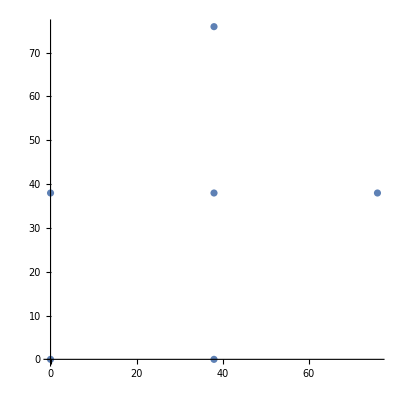

```mathematica
list=DeleteDuplicates[Take[#,2]&/@List[List[37.96270358973381,75.92540717946763,8713.259257897671],List[0.,37.96270358973381,8705.257610486882],List[37.96270358973381,37.96270358973381,8697.256352534716],List[75.92540717946763,37.96270358973381,8672.255093490214],List[0.,0.,8688.254700764901],List[37.96270358973381,0.,8667.253443386673],List[37.96270358973381,75.92540717946763,8662.652861935574],List[0.,37.96270358973381,8662.652861935574],List[37.96270358973381,37.96270358973381,8662.652861935574],List[75.92540717946763,37.96270358973381,8662.652861935574],List[0.,0.,8662.652861935574],List[37.96270358973381,0.,8662.652861935574]]//N];
ListPlot[list,AspectRatio->1]
```

```mathematica
Length@list
```

6

```mathematica
data=GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[100, "Kilometers"]]];
pic=ListPlot3D[Reverse[%],MeshFunctions->{#3&},Mesh->30]
```